(2 (1+4 x^2)+2 (1+4 y^2))/(2 (1+4 x^2+4 y^2)^(3/2))

-Graphics3D-

-Graphics3D-

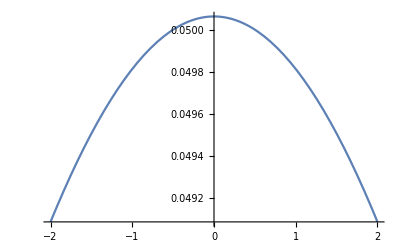

```mathematica
s[x_,y_]=x^2+y^2;
H[x_,y_]=((1+(D[s[x,y], x])^2)D[s[x,y], y,y]-2(D[s[x,y], x])(D[s[x,y], y])D[s[x,y], x,y]+(1+(D[s[x,y], y])^2)D[s[x,y], x,x])/(2(1+(D[s[x,y], x])^2+(D[s[x,y], y])^2)^(3/2))
Plot3D[s[x,y],{x,-2,2},{y,-2,2}]
Plot3D[H[x,y],{x,-2,2},{y,-2,2},PlotRange->All,PlotPoints->50]
Plot[H[x,10],{x,-2,2}]
```

```mathematica
(MS=({{1+(D[z[s1,s2], s1])^2, (D[z[s1,s2], s1])(D[z[s1,s2], s2])}, {(D[z[s1,s2], s1])(D[z[s1,s2], s2]), 1+(D[z[s1,s2], s2])^2}}))//MatrixForm
(MSS=Inverse[MS])//MatrixForm
A=Det[MS]
```

(1+(z^(1,0)[s1,s2])^2 | z^(0,1)[s1,s2] z^(1,0)[s1,s2]
z^(0,1)[s1,s2] z^(1,0)[s1,s2] | 1+(z^(0,1)[s1,s2])^2)

((1+(z^(0,1)[s1,s2])^2)/(1+(z^(0,1)[s1,s2])^2+(z^(1,0)[s1,s2])^2) | -(z^(0,1)[s1,s2] z^(1,0)[s1,s2])/(1+(z^(0,1)[s1,s2])^2+(z^(1,0)[s1,s2])^2)
-(z^(0,1)[s1,s2] z^(1,0)[s1,s2])/(1+(z^(0,1)[s1,s2])^2+(z^(1,0)[s1,s2])^2) | (1+(z^(1,0)[s1,s2])^2)/(1+(z^(0,1)[s1,s2])^2+(z^(1,0)[s1,s2])^2))

1+(z^(0,1)[s1,s2])^2+(z^(1,0)[s1,s2])^2

```mathematica
lapBel[F_]:=(1/(√A)∑_(α=1)^2 (D[(√A∑_(β=1)^2 (MSS[[α,β]]D[F, {s1,s2}[[β]]])), {s1,s2}[[α]]])//FullSimplify);
lapBel[F1[s1,s2]]
```

1/((1+(z^(0,1)[s1,s2])^2+(z^(1,0)[s1,s2])^2)^2)(-z^(0,2)[s1,s2] F1^(1,0)[s1,s2] z^(1,0)[s1,s2]-z^(0,2)[s1,s2] F1^(1,0)[s1,s2] (z^(1,0)[s1,s2])^3+F1^(0,2)[s1,s2] (1+(z^(1,0)[s1,s2])^2) (1+(z^(0,1)[s1,s2])^2+(z^(1,0)[s1,s2])^2)-2 z^(0,1)[s1,s2] z^(1,0)[s1,s2] F1^(1,1)[s1,s2]-2 (z^(0,1)[s1,s2])^3 z^(1,0)[s1,s2] F1^(1,1)[s1,s2]-2 z^(0,1)[s1,s2] (z^(1,0)[s1,s2])^3 F1^(1,1)[s1,s2]+2 z^(0,1)[s1,s2] F1^(1,0)[s1,s2] (z^(1,0)[s1,s2])^2 z^(1,1)[s1,s2]+F1^(2,0)[s1,s2]+2 (z^(0,1)[s1,s2])^2 F1^(2,0)[s1,s2]+(z^(0,1)[s1,s2])^4 F1^(2,0)[s1,s2]+(z^(1,0)[s1,s2])^2 F1^(2,0)[s1,s2]+(z^(0,1)[s1,s2])^2 (z^(1,0)[s1,s2])^2 F1^(2,0)[s1,s2]-(1+(z^(0,1)[s1,s2])^2) F1^(1,0)[s1,s2] z^(1,0)[s1,s2] z^(2,0)[s1,s2]-F1^(0,1)[s1,s2] z^(0,1)[s1,s2] (z^(0,2)[s1,s2] (1+(z^(1,0)[s1,s2])^2)-2 z^(0,1)[s1,s2] z^(1,0)[s1,s2] z^(1,1)[s1,s2]+(1+(z^(0,1)[s1,s2])^2) z^(2,0)[s1,s2]))

```mathematica
surfGrad[F_]:=Sum[MSS[[α,β]](D[{s1,s2,z[s1,s2]}, {s1,s2}[[α]]])D[F, {s1,s2}[[β]]],{α,1,2},{β,1,2}]
surfGrad[f[s1,s2]]/. 1+(Derivative[0,1][z][s1,s2])^2+(Derivative[1,0][z][s1,s2])^2->s//FullSimplify//MatrixForm
```

(((1+(z^(0,1)[s1,s2])^2) f^(1,0)[s1,s2]-f^(0,1)[s1,s2] z^(0,1)[s1,s2] z^(1,0)[s1,s2])/s
(-z^(0,1)[s1,s2] f^(1,0)[s1,s2] z^(1,0)[s1,s2]+f^(0,1)[s1,s2] (1+(z^(1,0)[s1,s2])^2))/s
(f^(0,1)[s1,s2] z^(0,1)[s1,s2]+f^(1,0)[s1,s2] z^(1,0)[s1,s2])/s)